# l’Hôpital’s Rule

We have studied the following three limits:

#### 1.

```mathematica
lim_(x->2) (x-2)/(x^2-4)=lim_(x->2) (x-2)/((x+2)(x-2))=lim_(x->2) 1/(x+2)=1/4
```

#### 2.

```mathematica
lim_(x->0) (sin(x))/x=1
```

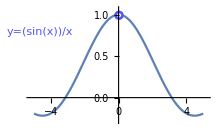

#### 3.

```mathematica
lim_(x->0) (1-cos(x))/x=0
```

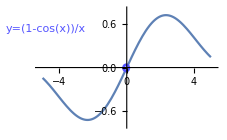

The first example we could calculate algebraically, but the last two we needed to calculate numerically from a graph, or use the Squeeze Theorem.

### Indeterminant Form

These limits are in Indeterminant Form, which evaluate to one of the following: 
0/0 or (±∞)/(±∞)

## The Rule

If a limit is in “indeterminant form,” then you can take the derivative of the numerator and denominator, and this new limit will evaluate to the same answer:

As x→a, if (f(x))/(g(x)) evaluates to 0/0 or (±∞)/(±∞), then:

```mathematica
lim_(x->a) (f(x))/(g(x))=lim_(x->a) (f'(x))/(g'(x))
```

Note that this not a method to find the derivative of a function, but a technique to evaluate a limit.

## The same three examples

### Take derivative of numerator & denominator, then evaluate:

#### 1.

```mathematica
lim_(x->2) (x-2)/(x^2-4)=lim_(x->2) 1/(2x)=1/(2(2))=1/4
```

#### 2.

```mathematica
lim_(x->0) (sin(x))/x= lim_(x->0) (cos(x))/1=1/1=1
```

#### 3.

```mathematica
lim_(x->0) (1-cos(x))/x=lim_(x->0) (sin(x))/1==0/1=0
```

Note that after taking the derivative of the numerator and denominator, the limits are no longer indeterminant and can be directly evaluated.

## Now You Try

### Practice 1

```mathematica
lim_(x->0) (sin(5 x))/(3 x)=
```

Write your answer here:

You can check your answer with this input cell. Click in the cell and press [shift] [enter]:

```mathematica
Limit[(Sin[5x])/(3x),x->0]
```

### Practice 2

```mathematica
lim_(x->1) (ln(x))/(x^2-x)=
```

Write your answer here:

You can check your answer with this input cell. Remember, you need to input Log[x] for ln(x):

### Practice 3

```mathematica
lim_(x->0) (ⅇ^(5 x)-1)/(3 x)=
```

Write your answer here:

You can check your answer with this input cell. Remember, you need to input Log[x] for ln(x):

### Practice 4 - You can use the Rule more than once:

```mathematica
lim_(x->0) (x-sin(x))/(cos(x)-1)=
```

Write your answer here:

You can check your answer with this input cell. Remember, you need to input Log[x] for ln(x):

## The actual author...

The rule is named after the 17th-century French mathematician Guillaume de l’Hôpital. Although the contribution of the rule is often attributed to L’Hôpital, the theorem was first introduced to L’Hôpital in 1694 by the Swiss mathematician Johann Bernoulli.    https://en.wikipedia.org/wiki/L%27 H % C3 % B4pital %27 s_rule

https://www.youtube.com/watch?v=7P7BsPvSVAs

## Authorship Information

Dan Uhlman
uhlmand@tas.tw